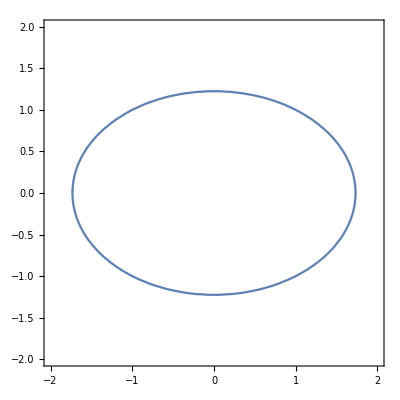

```mathematica
(*Лабораторная работа №2*)
(*По курсу «Защита информационных процессов в компьютерных системах»*)
(*Исследование свойств эллиптических кривых.*)

(*
	Кутузов Илья
	А-12м-20
*)

(*Задание 1*)
(*Построить график эллипса X^2+2*Y^2=3, используя ContourPlot[] пакета математки*)
AbsScaleX1=2;
AbsScaleY1=2;
ContourPlot[x^2+2*y^2==3,{x,-AbsScaleX1,AbsScaleX1},{y,-AbsScaleY1,AbsScaleY1}]
```

0

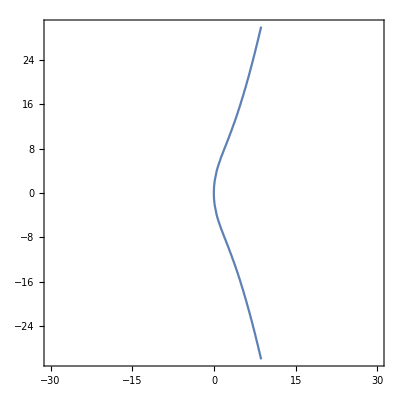

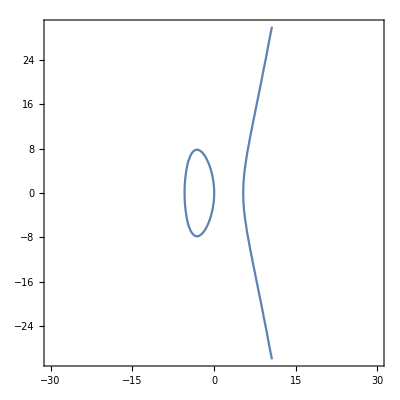

```mathematica
(*Задание 2*)
(*В поле рациональных чисел построить графики эллиптических кривых Y^2=X^3+a*X+b для положительного и отрицательного коэффициента a*)
a=29;
b=1;
c=0
p=31;
n=7;
AbsScaleX2=30;
AbsScaleY2=30;
ContourPlot[y^2==x^3+a*x+b,{x,-AbsScaleX2,AbsScaleX2},{y,-AbsScaleY2,AbsScaleY2}]
ContourPlot[y^2==x^3-a*x+b,{x,-AbsScaleX2,AbsScaleX2},{y,-AbsScaleY2,AbsScaleY2}]
```

```mathematica
(*Проверить выполенение условия гладкости кривой -16(4*a^3+27*b^2)≠0*)
-16*(4*a^3+27*b^2)≠0
```

True

```mathematica
(*Проверить, является ли заданный в правой части уравнения многочлен неприводимым, используя функцию Factor[]*)
Factor[x^3+a*x+b]
```

1+29 x+x^3

```mathematica
(*Задание 3*)
(*Проверить выполнение условия гладкости кривой в GF(p)*)
```

```mathematica
Mod[4*a^3+27*b^2,83]≠0
```

True

```mathematica
(*Определить число точек заданной кривой в поле GF(p)... *)
Clear[x,y]; 
g1={x,y}/.Flatten[Table[FindInstance[y^2==x^3+a*x+b  && x==u,{x,y},2,Modulus->p],{u,0,p-1}],1]
```

{{0,1},{0,30},{1,0},{2,6},{2,25},{6,9},{6,22},{7,12},{7,19},{8,1},{8,30},{10,12},{10,19},{11,15},{11,16},{12,0},{13,8},{13,23},{14,12},{14,19},{16,2},{16,29},{18,0},{19,8},{19,23},{20,5},{20,26},{23,1},{23,30},{25,13},{25,18},{26,14},{26,17},{27,10},{27,21},{29,11},{29,20},{30,8},{30,23}}

```mathematica
(*Длина полученного списка с учетом точки в бесконечности–порядок кривой*)
Length[g1]+1
```

40

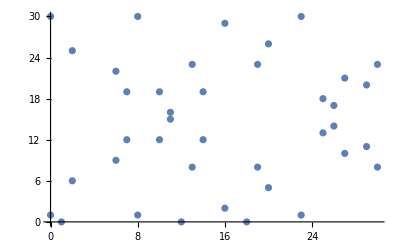

```mathematica
(*... и построить точеченый график*)
ListPlot[g1]
```

```mathematica
(*Задание 4*)
(*Сложить две точки, принадлежащие заданной эллиптической кривой, зафиксировать полученный результат на точеченом графике*)
(*Операцию сложения можно выполнить, используя следующий программный модуль*)
(*При использовании данного модуля следует учитывать,что он реализует сложение точек эллиптических кривых вида: y^2=x^3+ax^2+bx+c*)
```

```mathematica
EllipticAdd[p_,a_,b_,c_,P_List,Q_List]:=Module[{lam,x3,y3,P3},
Which[
P=={O},Q,
Q=={O},P,
P[[1]]≠Q[[1]],
	lam=Mod[(Q[[2]]-P[[2]]) PowerMod[Q[[1]]-P[[1]],p-2,p],p];
	x3=Mod[lam^2-a-P[[1]]-Q[[1]],p];
	y3=Mod[-(lam (x3-P[[1]])+P[[2]]),p];
	{x3,y3},
(P==Q)∧(P[[2]]==0),{O},
(P==Q)∧(P≠{O}),
	lam=Mod[(3*P[[1]]^2+2 a*P[[1]]+b) PowerMod[2 P[[2]],p-2,p],p];
	x3=Mod[lam^2-a-P[[1]]-Q[[1]],p];
	y3=Mod[-(lam (x3-P[[1]])+P[[2]]),p];
	{x3,y3},
(P[[1]]==Q[[1]])∧(P[[2]]≠Q[[2]]),{O}
]
]
EllipticAdd[a,b,c,p,g1[[4]],g1[[2]]]
```

{25,9}

```mathematica
(*Задание 5*)
(*Провести тестирование операции сложения,повторив следующие действия*)

ptest=11;
atest=0;
btest=6;
ctest=3;

{EllipticAdd[ptest,atest,btest,ctest,{4,6},{9,4}],
EllipticAdd[ptest,atest,btest,ctest,{9,4},{9,4}],
EllipticAdd[ptest,atest,btest,ctest,{4,6},{4,6}],
EllipticAdd[ptest,atest,btest,ctest,{4,6},{O}],
EllipticAdd[ptest,atest,btest,ctest,{4,6},{4,5}],
EllipticAdd[ptest,atest,btest,ctest,{O},{9,4}]}
```

{{3,9},{7,6},{4,5},{4,6},{O},{9,4}}

{{26,14},{23,1},{20,26},{18,0},{20,5},{23,30}}

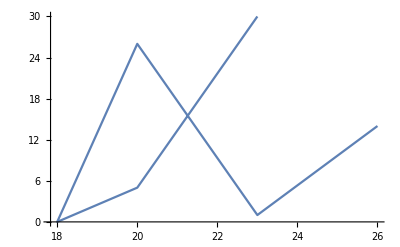

```mathematica
(*Задание 7*)
(*Провести операцию умножения произвольной точки на число n (Табл.1) и построить граф переходов.*)

Mult[p1_,a1_,b1_,c1_,point1_,num1_]:=Module[{p=p1,a=a1,b=b1, c=c1,point=point1,num=num1}, temp=point;
q={};
Do[temp=EllipticAdd[p,a,b,c,point,temp];AppendTo[q,temp],{i,2,num}];
q];
path=Mult[p,0,a,b,g1[[8]],n]
ListLinePlot[path]
```

```mathematica
(*Задание 8*)
(*Для каждой точки заданной кривой определить её порядок (Определение:Порядком точки Р эллиптической кривой называется наименьшее натуральное число m≠0,для которого mР=О.См.также articles\osnovy_elliptic.pdf,page 69).Построить гистограмму распределения порядков точек.*)
Mult2[p1_,a1_,b1_,c1_,point1_,num1_]:=Module[{p=p1,a=a1,b=b1, c=c1,point=point1,num=num1}, temp=point;
q={};
Do[temp=EllipticAdd[p,a,b,c,point,temp];AppendTo[q,temp],{i,2,num}];
temp];
```

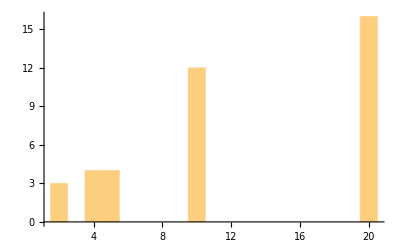
{{{4,4},{2,3},{10,12},{20,16},{5,4}},-Graphics-}

```mathematica
s={};i=1;
For[j=1,j≤Length[g1],j++,{
While[Mult2[p,0,a,b,g1[[j]],i]!=  {O},i++],AppendTo[s,i],i=1}];{Tally[s],Histogram[s,Length[g1]]}
```